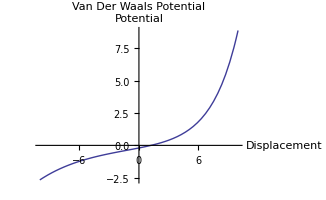

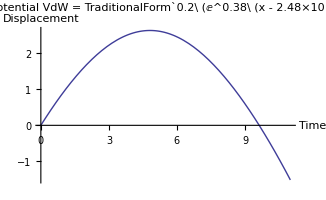

```mathematica
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["FunctionApproximations`"];
a=2.48*10^-12;
b=0.19;
Dw=0.2;
VdW=Dw*(Exp[2*b(x-a)]-2*Exp[-b*(x-a)]);
Plot[VdW,{x,-10,10},PlotRange->All,PlotLabel->"Van Der Waals Potential",AxesLabel->{"Displacement","Potential"}]

EqMot=m1*x1''[t]+D[VdW/.x->x1[t],x1[t]]==0;

m1=1;
sol=NDSolve[{EqMot,x1[0]==0,x1'[0]==1},x1,{t,0,10},MaxSteps->∞, Method->"StiffnessSwitching",AccuracyGoal->14,PrecisionGoal->14];
Plot[Evaluate[x1[t]/.sol],{t,0,11},PlotLabel->StringJoin["Motion of one Particle Under Morse Potential \n VdW = ",ToString[VdW//TraditionalForm]],AxesLabel->{"Time","Displacement"}]
```

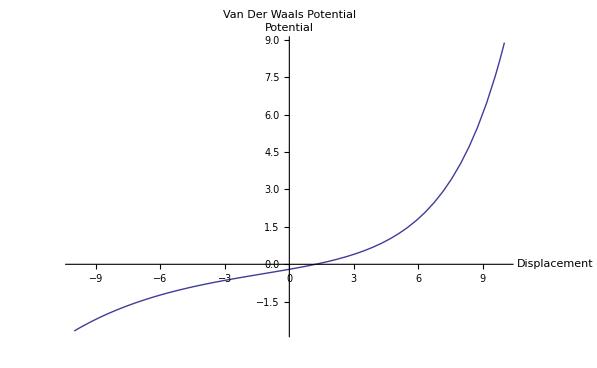

0.5 (x1'[t]^2+x2'[t]^2+x3'[t]^2)

0.2 (-2 ⅇ^(-0.19 (-2.48×10^-12+x1[t]))+ⅇ^(0.38 (-2.48×10^-12+x1[t])))+0.2 (-2 ⅇ^(-0.19 (-2.48×10^-12-x1[t]+x2[t]))+ⅇ^(0.38 (-2.48×10^-12-x1[t]+x2[t])))+0.2 (-2 ⅇ^(-0.19 (-2.48×10^-12-x2[t]+x3[t]))+ⅇ^(0.38 (-2.48×10^-12-x2[t]+x3[t])))

NDSolve::ndsz: At t == 20.3773, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

```mathematica
"VAN DER WAALS"
"
    1 J·m3/mol2 = 1 m6·Pa/mol2 = 10 L2·bar/mol2
    1 m3/mol = 1000 L/mol 
a (L2bar/mol2)↓b (L/mol)↓

Acetic acid 17.82 0.1068
Acetic anhydride 20.16 0.1263
Acetone 14.09 0.0994
Acetonitrile 17.81 0.1168
Acetylene 4.448 0.05136
Ammonia 4.225 0.03707
Argon 1.363 0.03219
Benzene 18.24 0.1154
Bromobenzene 28.94 0.1539
Butane 14.66 0.1226
Carbon dioxide 3.640 0.04267
Carbon disulfide 11.77 0.07685
Carbon monoxide 1.505 0.03985
Carbon tetrachloride 19.7483 0.1281
Chlorine 6.579 0.05622
Chlorobenzene 25.77 0.1453
Chloroethane 11.05 0.08651
Chloromethane 7.570 0.06483
Cyanogen 7.769 0.06901
Cyclohexane 23.11 0.1424
Diethyl ether 17.61 0.1344
Diethyl sulfide 19.00 0.1214
Dimethyl ether 8.180 0.07246
Dimethyl sulfide 13.04 0.09213
Ethane 5.562 0.0638
Ethanethiol 11.39 0.08098
Ethanol 12.18 0.08407
Ethyl acetate 20.72 0.1412
Ethylamine 10.74 0.08409
Fluorobenzene 20.19 0.1286
Fluoromethane 4.692 0.05264
Freon 10.78 0.0998
Germanium tetrachloride 22.90 0.1485
Helium 0.03457 0.0237
Hexane 24.71 0.1735
Hydrogen 0.2476 0.02661
Hydrogen bromide 4.510 0.04431
Hydrogen chloride 3.716 0.04081
Hydrogen selenide 5.338 0.04637
Hydrogen sulfide 4.490 0.04287
Iodobenzene 33.52 0.1656
Krypton 2.349 0.03978
Mercury 8.200 0.01696
Methane 2.283 0.04278
Methanol 9.649 0.06702
Neon 0.2135 0.01709
Nitric oxide 1.358 0.02789
Nitrogen 1.408 0.03913
Nitrogen dioxide 5.354 0.04424
Nitrous oxide 3.832 0.04415
Oxygen 1.378 0.03183
Pentane 19.26 0.146
Phosphine 4.692 0.05156
Propane 8.779 0.08445
Silane 4.377 0.05786
Silicon tetrafluoride 4.251 0.05571
Sulfur dioxide 6.803 0.05636
Tin tetrachloride 27.27 0.1642
Toluene 24.38 0.1463
Water 5.536 0.03049
Xenon 4.250 0.05105"

a=2.48*10^-12;
b=0.19;
Dw=0.2;
VdW=Dw*(Exp[2*b(x-a)]-2*Exp[-b*(x-a)]);
Plot[VdW,{x,-10,10},PlotRange->All,PlotLabel->"Van Der Waals Potential",AxesLabel->{"Displacement","Potential"}]

T=0.5*(m1*x1'[t]^2+m2*x2'[t]^2+m3*x3'[t]^2)
V=(VdW/.x->x1[t])+(VdW/.x->(x2[t]-x1[t]))+(VdW/.x->(x3[t]-x2[t]))
L=T-V;
VdW3DOFEqs={
D[D[L,x1'[t]],t]-D[L,x1[t]]==Sin[3t],
D[D[L,x2'[t]],t]-D[L,x2[t]]==Sin[2t],
D[D[L,x3'[t]],t]-D[L,x3[t]]==Sin[t]
};
vars={x1,x2,x3};
initcon={x1[0]==0,x2[0]==0,x3[0]==0,x1'[0]==1,x2'[0]==0,x3'[0]==0};
flatted=Join[VdW3DOFEqs,initcon];

m1=m2=m3=1;
sol3DOF=NDSolve[flatted,vars,{t,0,200},MaxSteps->∞, Method->"StiffnessSwitching",AccuracyGoal->14,PrecisionGoal->14];
Plot[Evaluate[{x1[t],x2[t],x3[t]}/.sol3DOF],{t,0,200},PlotRange->All,PlotLabel->StringJoin["Motion of one Particle Under Morse Potential \n VdW = ",ToString[VdW//TraditionalForm]],AxesLabel->{"Time","Displacement"}]
```